# Learning Fourier Series in Mathematica

## April 24, 2019

Kirk Boyd
PHYS 300 - Walden

## Are these basis functions orthogonal? Are they orthonormal?

### Enter subsection title here

#### a.)

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
Subscript[u, n]=E^(I*(n*Pi*x)/L)
```

ⅇ^((ⅈ n π x)/L)

```mathematica
Subscript[u, m]=E^(I*(m*Pi*x)/L)
```

ⅇ^((ⅈ m π x)/L)

```mathematica
Assuming[n∈Integers&&m∈Integers&&L>0,∫_-L^L Conjugate[Subscript[u, n]]*Subscript[u, m] ⅆx]
```

0

```mathematica
Assuming[n∈Integers&&m∈Integers&&L>0,∫_-L^L Conjugate[Subscript[u, m]]*Subscript[u, n] ⅆx]
```

0

```mathematica
Assuming[n∈Integers&&L>0,∫_-L^L E^(-I*(n*Pi*x)/L)*E^(I*(n*Pi*x)/L)ⅆx]
```

2 L

```mathematica
Assuming[L>0,f[x_]=Abs[Sin[(Pi*x)/(2L)]]]
```

Abs[Sin[(π x)/(2 L)]]

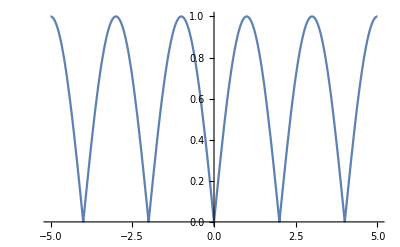

```mathematica
L=1;
Plot[f[x],{x,-5L,5L}]
```

```mathematica
Assuming[n∈Integers,Subscript[c, n][n_]=(∫_-L^L E^(I*(Pi*n*x)/L)*f[x]ⅆx)/2L]
```

-2/((-1+4 n^2) π)

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}